```mathematica
areaOfDetector=(19/1000)^2; (* 19mm x 19mm *)
areaOfAperture=(16*(4+Pi))/1000^2; (*8mm x 16mm with rounded edges *)
detectorFieldOfViewDiameter=2*Degree;
detectorFieldOfViewSolidAngle=2*Pi*(1-Cos[detectorFieldOfViewDiameter/2]);

directory="/home/sidney/Repositories/github/MitsubaARCF/arcf-model";
```

## Process Irradiance Measurement

```mathematica
irradianceFilename=FileNameJoin[{directory,"arcf-irradiance.m"}];

irradiance=Block[{detector},Get[irradianceFilename];detector];

signalIrradiance=Mean[Flatten[irradiance]];

(* 'powerPerAreaIrradiance' [W/m^2] should be equal to the exitance of the emitter. *)
powerPerAreaIrradiance=signalIrradiance*areaOfDetector/areaOfAperture;
```

```mathematica
Print["Dimensions: ",Dimensions[irradiance]]
Print["signalIrradiance: ",signalIrradiance]
Print["powerPerAreaIrradiance: ",powerPerAreaIrradiance]
```

Dimensions: {256,256}

signalIrradiance: 0.3164654126101692561791851589

powerPerAreaIrradiance: 0.9998121173192124118220796707

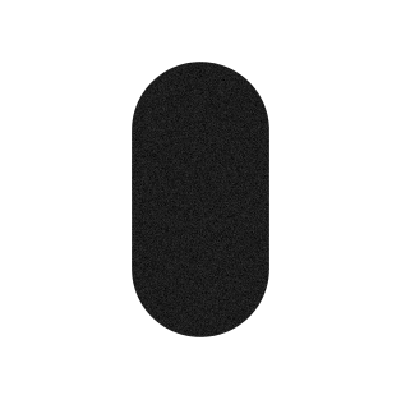

```mathematica
ArrayPlot[irradiance,PlotRange->All]
```

```mathematica
ListPlot3D[irradiance,PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[LowpassFilter[irradiance,1/10],PlotRange->All]
```

-Graphics3D-

## Process Radiance Measurement

```mathematica
radianceFilename=FileNameJoin[{directory,"../arcf-model-bug/arcf-ok.m"}];
radianceFilename=FileNameJoin[{directory,"../test-fieldfocus.m"}];

radiance=Block[{detector},Get[radianceFilename];detector];

signalRadiance=Mean[Flatten[radiance]];
```

```mathematica
Print["Dimensions: ",Dimensions[irradiance]]
Print["signalRadiance: ",signalIrradiance]
```

Dimensions: {256,256}

signalRadiance: 0.3164654126101692561791851589

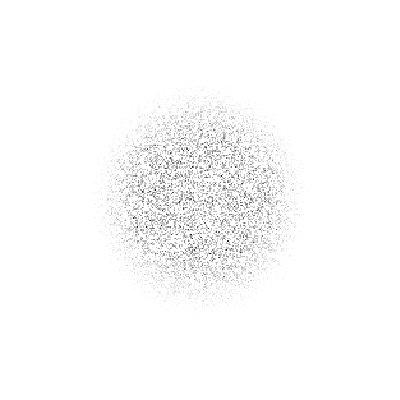

```mathematica
ArrayPlot[radiance,PlotRange->All]
```

```mathematica
ListPlot3D[radiance,PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[LowpassFilter[radiance,1/10],PlotRange->All]
```

-Graphics3D-

## Calclulate BSDF

```mathematica
bsdfPerfect=N[1/Pi,30]
bsdfEstimate=(signalRadiance/signalIrradiance)/detectorFieldOfViewSolidAngle
```

0.318309886183790671537767526745

4.313254985464401221763803336×10^-7

```mathematica
bsdfEstimate/bsdfPerfect
```

1.355049017539451329752957927×10^-6